# Generating Random Gaussian States

#### Initialization

```mathematica
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"]
LoadPlotStyling[];

Needs["MaTeX`"];
SetOptions[MaTeX,
"Preamble"->{"
\\usepackage{xcolor,txfonts} 
\\usepackage{amsmath}
\\DeclareMathOperator*{\\argmax}{arg\\,max}
\\DeclareMathOperator*{\\argmin}{arg\\,min}
\\definecolor{royalpurple}{HTML}{7851a9}
\\definecolor{RoyalBlue}{rgb}{0.25, 0.41, 0.88}
"}];
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

/home/gabriel/Nextcloud/Cluster/Wolfram Mathematica/Mathematica Images/

https://mathematica.stackexchange.com/questions/6355/how-can-one-define-an-infix-operator-with-an-arbitrary-unicode-character

```mathematica
(*Defines an arbitrary binary operation with Infix*)

MakeExpression[RowBox[{x_,"⊞",y_}],StandardForm]:=MakeExpression[RowBox[{"FlatJoin","[",x,",",y,"]"}],StandardForm]

FlatJoin/:MakeBoxes[FlatJoin[x_,y_],StandardForm]:=RowBox[{MakeBoxes[x,StandardForm],"⊞",MakeBoxes[y,StandardForm]}]
```

### Random Quantum Covariance Matrix

We first define the symplectic form:

```mathematica
J[n_]:=KroneckerProduct[IdentityMatrix[n/2],({{0, 1}, {-1, 0}})];
J[4]//MatrixForm
Eigenvalues@(ⅈ %)
```

(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

{-1,-1,1,1}

And GOE matrices with variance σ^2:

```mathematica
ClearAll[GOE]
G[n_,σ_:1]:=1/(√n)RandomVariate@GaussianOrthogonalMatrixDistribution[σ, 2n];
G[1]//MatrixForm
```

(-0.47541 | 0.715464
0.715464 | -1.57791)

Generating Random Gaussian States

The ensemble of Random Quantum Covariance Matrices (RQCM), denoted by RQCM(2n, σ), has elements:

S_G := G + λ_max[i J_(2n) - G]I_(2n)
 
 There G is drawn from the GOE ensemble G ∈ GOE(2n, σ) and J_(2n)  is the symplectic form defined above.

```mathematica
(*Finds the closest valid CM to G*)
ClosestGaussian[G_]:=With[{λ=Max@Eigenvalues[ⅈ J[Length@G]-G]},
G+Max@{0,λ }IdentityMatrix[Length@G]
]

(*Generates a RQCM*)
RQCM[n_, σ_:1]:=ClosestGaussian[G[n,σ]]
```

Validity of Gaussian states: 

A valid CM should obey

S + i J_(2n) ≥ 0,

which we can express in terms of its minimum eigenvalue. Namely, it should be larger than or equal than zero.

```mathematica
GaussianQ[G_]:=Min@Eigenvalues[G+ⅈ J[Length@G]];
```

So, consider the GOE matrix:

```mathematica
Subscript[G, 0]=G[1];Subscript[G, 0]//MatrixForm
```

(1.11001 | -0.879306
-0.879306 | 0.414621)

This is not a valid CM, since we have:

```mathematica
GaussianQ@Subscript[G, 0]
```

-0.613936

However, by properly shifting it, we get a valid Gaussian state:

```mathematica
H=ClosestGaussian@Subscript[G, 0];H//MatrixForm

(*Smallest eigenvalue of H - Subscript[iJ, 2n], should be non-negative*)
Chop@GaussianQ@H
```

(1.72395 | -0.879306
-0.879306 | 1.02856)

0

### Eigenvalues of the RQCM ensemble

For convenience we define the “numerical Free Convolution”:

```mathematica
A_ ⊞ B_:=Eigenvalues[A+B];
```

In order to find the distribution of eigenvalues in the QRCM ensemble, we compute the convolution (numerically) of three different GOE matrices with the symplectic form -- changing σ:

```mathematica
n = 1000;
Subscript[μ, σ]=G[n,#]⊞ (ⅈ J[2n])&/@{2,1,0.5};
```

Analytically, the distribution looks like:

```mathematica
R[σ_]:=(1+σ/4(√(8+σ^2)-σ))√(1+σ/2(√(8+σ^2)+σ));
DSc[x_,σ_]:=((√(4 σ^2-(x-m)^2))/(2π σ^2)Boole[Abs[x-m]<2σ])/.(m-> R[σ]);
```

By doing so, we get:

```mathematica
GaussianMeasurePlot=Show[
Histogram[
Subscript[μ, σ]
,{"Raw",50}
,"PDF" (*PDF and not probability here*)
,Frame->True
,FrameLabel->{MaTeX["x",Magnification->1.5],MaTeX["\\mu_\\sigma(x)",Magnification->1.5]}
,PlotRangeClipping->False
,LabelStyle->Directive[Black,FontFamily->"Times", 14]
,ChartStyle->{RGBColor[0.32,0.7,0.34],RGBColor[0.5,0.27,0.5],RGBColor[1,0.51,0.5]}
,ImageSize->400
,PlotRange->{0,0.5}
,ChartLegends->Placed[SwatchLegend[{MaTeX[StringTemplate["`1`"][#],Magnification-> 1.25]&/@{"2","1","0.5"}},LegendLabel->MaTeX["\\sigma",Magnification-> 1.5]],{1.0,0.5}]
]
(*,Plot[DSc[x,#]&/@{2,1,0.5}//Evaluate
,{x,-5,5}
,PlotStyle->{RGBColor[0.32,0.7,0.34],RGBColor[0.5,0.27,0.5],RGBColor[1,0.51,0.5]}
]*)
]
```

-Graphics-

Measure of the QRCMs: 

Since the symplectic form has just eigenvalues +1 or -1, it works as a “Bernoulli distribution”, and the result above corresponds to the convolution:

(1/2 δ_1 +1/2 δ_-1) ⊞ SC_σ, where SC_σ is the semicircular distribution SC_σ := (√(4 σ^2-(x-m)^2))/(2π σ^2)1_(|x<2σ|)(x)dx.

The analytical result can be obtained by using the Stieltjes’ inversion formula from the R-transform obtained from this problem:

ℛ_μ_σ(z) = ℛ_Bernoulli(z) + ℛ_SC_σ(z) = (√(1 + 4 z^2) -1)/(2z)+ σ z.

which lead us to some complicated cubic roots.

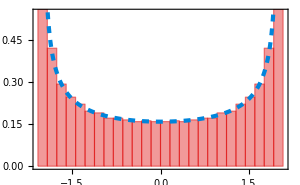
Very interestingly, we can see that we have “phase-transition” on the support of the matrices of this example at σ = 1. One has:

• Support on two intervals for σ > 1
• Support on a single interval for  σ < 1

Note that a similar convolution with CUE instead of GOE matrices leads to a very different distribution. Namely, the arcsine distribution:

-Graphics-
This arises, for example, when one computes the eigenvalues of U A U † + B, with A and B being diagonal and deterministic and U being a CUE element.

One of the useful things we can do with these results is to compute a few relevant quantities from the RQCM. For instance, let us consider the purity:

```mathematica
𝒫[S_]:=1/(√Det[S]);
```

We compute it for σ = 0.5 and σ = 2:

```mathematica
PurityListA=𝒫/@(RQCM[#, 0.5]&/@Range[1,30]);
PurityListB=𝒫/@(RQCM[#, 2]&/@Range[1,30]);
```

Purity of the QRCM: 

For a normalized RQCM(2n, σ/(√(2n))), we can define the quantity:

LD(σ) := ∫_(R(σ) - 2σ)^(R(σ) + 2σ) ln(x) dSC_(R(σ), σ)(x);

such that, for asymptotic n, we have

-1/nlog 𝒫(S)  → LD(σ). Or, equivalently:

𝒫(S)   ~ e^(-n LD(σ))

The dashed lines correspond to the analytical prediction:

```mathematica
LD[σ_]:=NIntegrate[Log[x]DSc[x,σ],{x,R[σ]-2σ, R[σ]+2σ}]
```

```mathematica
ldA=LD[0.5];
ldB=LD[2];
Show[
(*Numerics*)
ListLogPlot[
{PurityListA,PurityListB}
,Joined->True
,PlotStyle->{RGBColor[0.32,0.7,0.34],RGBColor[1,0.51,0.5]}
,FrameTicks->{{logticks[-20,2,3],Automatic},{Automatic,Automatic}}
,FrameLabel->{MaTeX["n",Magnification-> 2],MaTeX["\\mathcal{P}(S_\\rho)",Magnification-> 2]}
,PlotLegends->Placed[SwatchLegend[
MaTeX[StringTemplate["`1`"][#],Magnification-> 1.25]&/@{"0.5","2"}
,LegendLabel->MaTeX["\\sigma",Magnification-> 1.5]]
,{1.0,0.5}
]
,ImageSize->400
],

(*Analytics*)
LogPlot[
{Exp[-n ldA],Exp[-n ldB]}
,{n,1,30}
,PlotStyle-> {{Black,Dashed},{Black,Dashed}}
]
]
```

-Graphics-

Finally, in the paper they also provide analytical computations for the symplectic eigenvalues  from the 𝒮-transform. We omit that part here and show only the numerics. Nevertheless, this computation is useful be cause 

i) it immediately provides an energy upper bound for the CM, and

ii) also provides insight in any quantities which might depend on them.

See a review on: https://arxiv.org/pdf/2106.11965. 

- A pedagogical tutorial on symplectic eigenvalues ν_i and derivations can be found here: https://markwilde.com/teaching/2019-spring-gqi/scribe-notes/lecture-10-scribed.pdf

```mathematica
Show[
Histogram[
SymplecticEigenvalues@RQCM[500,#]&/@{2,1,0.5}
,{"Raw",50}
,"PDF" (*PDF and not probability here*)
,Frame->True
,FrameLabel->{MaTeX["x",Magnification->1.5],MaTeX["\\nu_i",Magnification->1.5]}
,PlotRangeClipping->False
,LabelStyle->Directive[Black,FontFamily->"Times", 14]
,ChartStyle->{RGBColor[0.32,0.7,0.34],RGBColor[0.5,0.27,0.5],RGBColor[1,0.51,0.5]}
,ImageSize->400
,PlotRange->{0,1}
,ChartLegends->Placed[SwatchLegend[{MaTeX[StringTemplate["`1`"][#],Magnification-> 1.25]&/@{"2","1","0.5"}},LegendLabel->MaTeX["\\sigma",Magnification-> 1.5]],{1.0,0.5}]
]
]
```

-Graphics-

Note that the smaller the value of σ, the more concentrated the symplectic eigenvalues are around 1, and the purer the state is.